```mathematica
(* Jenny Chen *)
(* MATH2262 Analytic Geometry and Calculus II *)
(* Mathematica Project II *)

(* Pg. 494, # 65-67*)

(* 65. *)
(* a. ∫x Log[E, x]ⅆx *)
Integrate[x Log[E,x],x]
```

-x^2/4+1/2 x^2 Log[x]

```mathematica
(* b. ∫x^2 Log[E, x]ⅆx *)
Integrate[x^2 Log[E,x], x]
```

-x^3/9+1/3 x^3 Log[x]

```mathematica
(* c. ∫x^3 Log[E, x]ⅆx *)
Integrate[x^3 Log[E,x], x]
```

-x^4/16+1/4 x^4 Log[x]

```mathematica
(* 66. *)
(* a. ∫Log[E, x]/x^2 ⅆx *)
Integrate[Log[E,x]/ x^2, x]
```

-1/x-Log[x]/x

```mathematica
(* b. ∫Log[E, x]/x^3 ⅆx *)
Integrate[Log[E, x]/ x^3, x]
```

-1/(4 x^2)-Log[x]/(2 x^2)

```mathematica
(* c. ∫Log[E, x]/x^4 ⅆx *)
Integrate[Log[E, x]/ x^4, x]
```

-1/(9 x^3)-Log[x]/(3 x^3)

```mathematica
(* d. ∫Log[E, x]/x^5 ⅆx *)
Integrate[Log[E,x]/ x^5, x]
```

-1/(16 x^4)-Log[x]/(4 x^4)

```mathematica
(* 67. ∫_0^(π/2) Sin[x]^n/(Sin[x]^n+Cos[x]^n)ⅆx *)
(* n = 1 *)
Integrate[(Sin[x]^1/(Sin[x]^1 + Cos[x]^1)),{x, 0, Pi/2}]
```

π/4

```mathematica
(* n = 2 *)
Integrate[(Sin[x]^2/(Sin[x]^2 + Cos[x]^2)),{x, 0, Pi/2}]
```

π/4

```mathematica
(* n = 3 *)
Integrate[(Sin[x]^3/(Sin[x]^3 + Cos[x]^3)),{x, 0, Pi/2}]
```

π/4

```mathematica
(* n = 5 *)
Integrate[(Sin[x]^5/(Sin[x]^5 + Cos[x]^5)),{x, 0, Pi/2}]
```

π/4

```mathematica
(* n = 7 *)
Integrate[(Sin[x]^7/(Sin[x]^7 + Cos[x]^7)),{x, 0, Pi/2}]
```

π/4

```mathematica
(* Pg. 515, # 81-86 *)
(* 81. ∫_0^ⅇ x^p Log[E, x]ⅆx *)
Table[{p,NIntegrate[x^p Log[E,x],{x,0,ⅇ}]},{p,2,10,0.5}]
```

{{2.,4.46345},{2.5,6.75826},{3.,10.2372},{3.5,15.5585},{4.,23.7461},{4.5,36.4005},{5.,56.0318},{5.5,86.5865},{6.,134.282},{6.5,208.929},{7.,326.042},{7.5,510.184},{8.,800.305},{8.5,1258.26},{9.,1982.38},{9.5,3129.23},{10.,4948.28}}

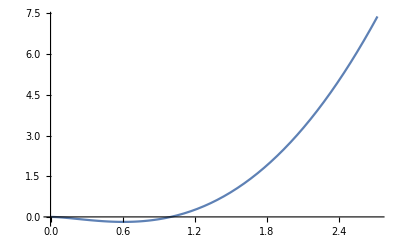
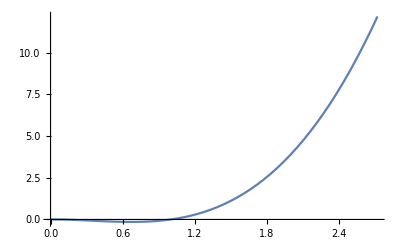
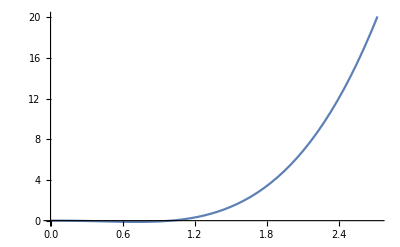
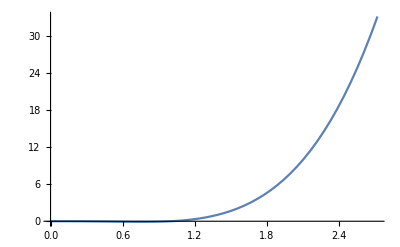
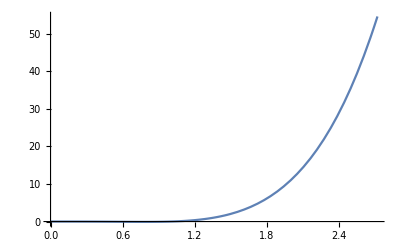
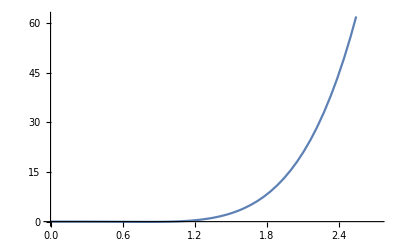
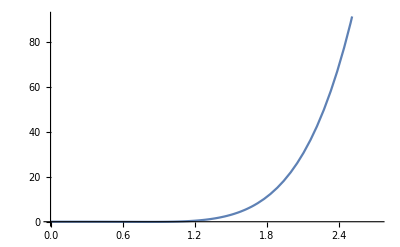
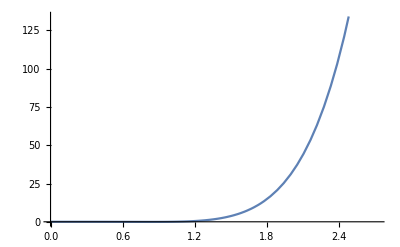
{{2.,-Graphics-},{2.5,-Graphics-},{3.,-Graphics-},{3.5,-Graphics-},{4.,-Graphics-},{4.5,-Graphics-},{5.,-Graphics-},{5.5,-Graphics-},{6.,-Graphics-},{6.5,-Graphics-},{7.,-Graphics-},{7.5,-Graphics-},{8.,-Graphics-},{8.5,-Graphics-},{9.,-Graphics-},{9.5,-Graphics-},{10.,-Graphics-}}

```mathematica
Table[{p,Plot[x^p Log[E,x],{x,0,ⅇ},AxesOrigin->{0,0}]},{p,2,10,0.5}]
```

```mathematica
(* 82. ∫_ⅇ^∞ x^p Log[E, x]ⅆx *)
Table[{p,NIntegrate[x^p Log[E,x],{x, ⅇ, Infinity}]},{p,2,15,.6}]
```

{{2.,1.37249936431823×10^83844},{2.6,9.03909624555908×10^100610},{3.2,5.95302723360052×10^117377},{3.8,3.92058368217261×10^134144},{4.4,2.58204369089767×10^150911},{5.,1.70049925250768×10^167678},{5.6,1.11992594011535×10^184445},{6.2,7.37568163918143×10^201211},{6.8,4.85752474255469×10^217978},{7.4,3.19910047334639×10^234745},{8.,2.10688455173449×10^251512},{8.6,1.38756583320978×10^268279},{9.2,9.13832198413647×10^285045},{9.8,6.01837597085938×10^301812},{10.4,3.96362148163284×10^318579},{11.,2.61038780686992×10^335346},{11.6,1.71916630612637×10^352113},{12.2,1.13221981053617×10^368880},{12.8,7.45664741655058×10^385646},{13.4,4.91084771502274×10^402413},{14.,3.2342182663238×10^419180},{14.6,2.13001265769374×10^435947}}

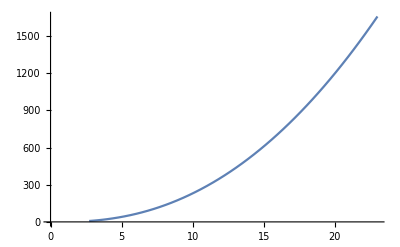
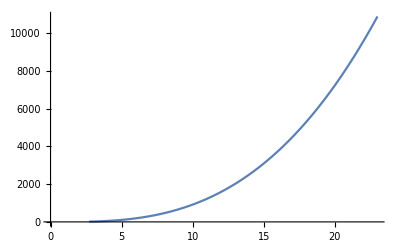
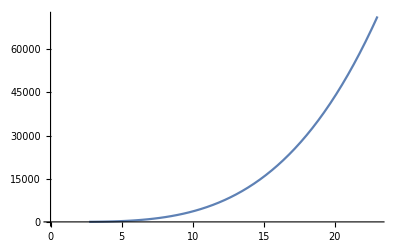
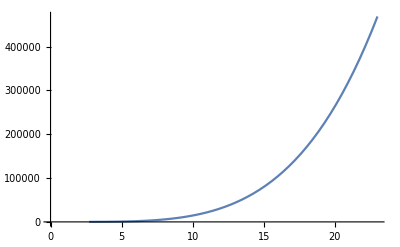
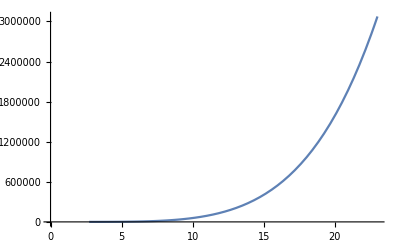
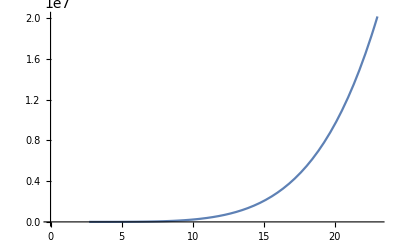
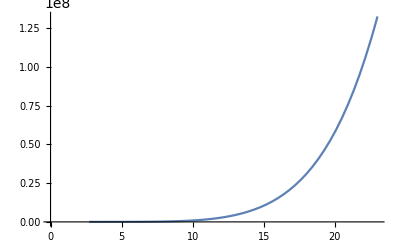
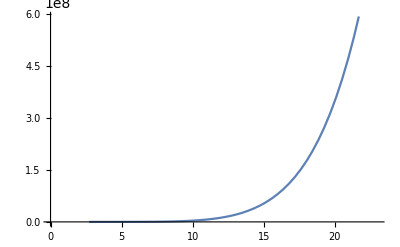
{{2.,-Graphics-},{2.6,-Graphics-},{3.2,-Graphics-},{3.8,-Graphics-},{4.4,-Graphics-},{5.,-Graphics-},{5.6,-Graphics-},{6.2,-Graphics-},{6.8,-Graphics-},{7.4,-Graphics-},{8.,-Graphics-},{8.6,-Graphics-},{9.2,-Graphics-},{9.8,-Graphics-},{10.4,-Graphics-},{11.,-Graphics-},{11.6,-Graphics-},{12.2,-Graphics-},{12.8,-Graphics-},{13.4,-Graphics-},{14.,-Graphics-},{14.6,-Graphics-}}

```mathematica
Table[{p,Plot[x^p Log[E,x],{x ,ⅇ, 23},AxesOrigin->{0,0}]},{p,2,15, .6}]
```

```mathematica
(* 83. ∫_0^∞ x^p Log[E, x]ⅆx *)
Table[{p,NIntegrate[x^p Log[x],{x, 0, Infinity}]},{p, 0, 5, .3}]
```

{{0.,5.52250294797429×10^27954},{0.3,1.41723668581121×10^36338},{0.6,3.63704617730609×10^44721},{0.9,9.33373022879439×10^53104},{1.2,2.39530970295074×10^61488},{1.5,6.14706921276377×10^69871},{1.8,1.57751875924061×10^78255},{2.1,4.04837712042905×10^86638},{2.4,1.03893264106894×10^95022},{2.7,2.666206730594×10^103405},{3.,6.84227066286468×10^111788},{3.3,1.75592789881323×10^120172},{3.6,4.50622744650387×10^128555},{3.9,1.15643050119147×10^136939},{4.2,2.96774079862197×10^145322},{4.5,7.6160957690223×10^153705},{4.8,1.95451418106424×10^162089}}

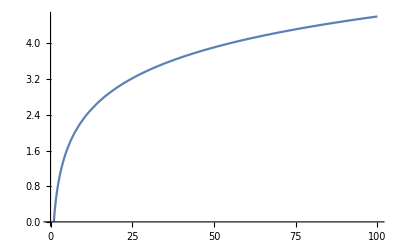
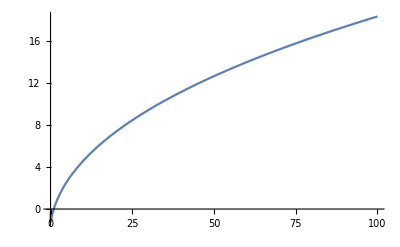
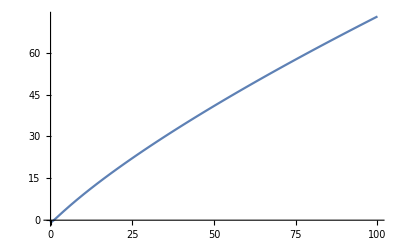
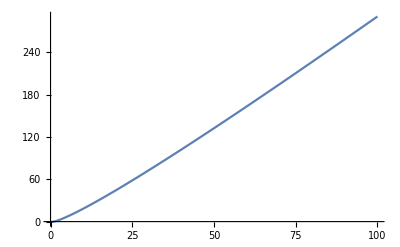
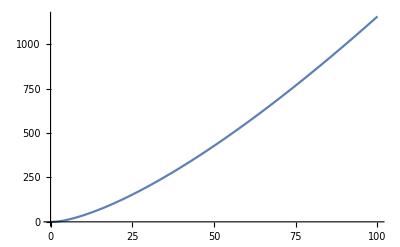
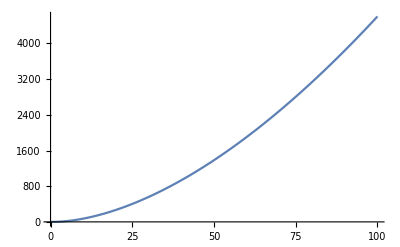
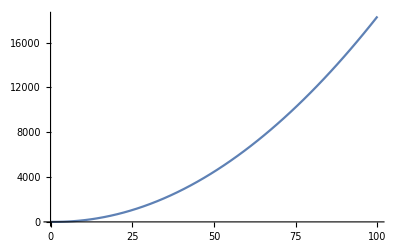
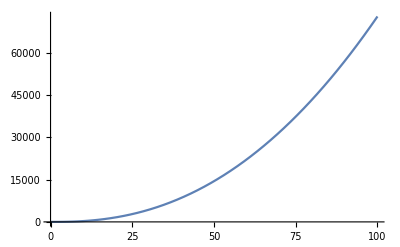
{{0.,-Graphics-},{0.3,-Graphics-},{0.6,-Graphics-},{0.9,-Graphics-},{1.2,-Graphics-},{1.5,-Graphics-},{1.8,-Graphics-},{2.1,-Graphics-},{2.4,-Graphics-},{2.7,-Graphics-},{3.,-Graphics-},{3.3,-Graphics-},{3.6,-Graphics-},{3.9,-Graphics-},{4.2,-Graphics-},{4.5,-Graphics-},{4.8,-Graphics-}}

```mathematica
Table[{p,Plot[x^p Log[E,x],{x,0, 100},AxesOrigin->{0,0}]},{p,0,5,.3}]
```

```mathematica
(* 84. ∫_(-∞)^∞ x^p Log[E, Abs[x]]ⅆx *)
Table[{p,NIntegrate[x^p Log[E, Abs[x]],{x, -Infinity, Infinity}]},{p,-1,2,0.5}]
```

{{-1.,1.12412×10^10},{-0.5,2.47338605258768×10^13982},{0.,1.10450058959486×10^27955},{0.5,1.23304806293694×10^41927},{1.,2.75311310801605×10^55899},{1.5,6.14706921275741×10^69871},{2.,1.37249936431634×10^83844}}

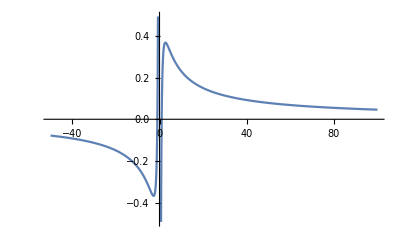
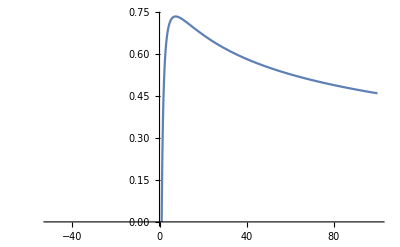
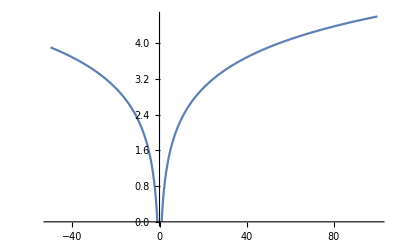
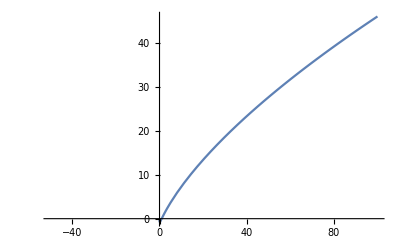
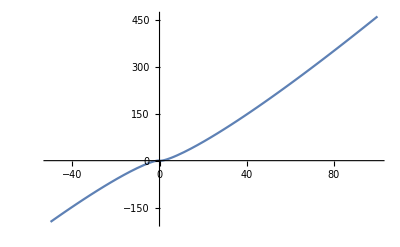
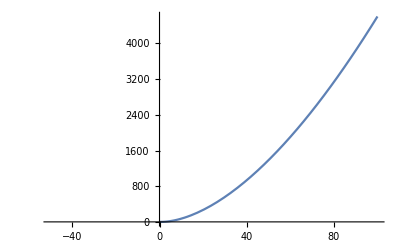
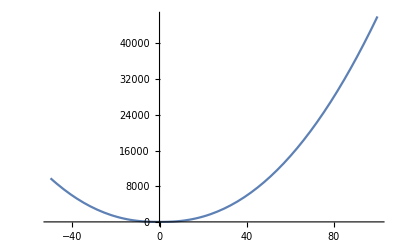
{{-1.,-Graphics-},{-0.5,-Graphics-},{0.,-Graphics-},{0.5,-Graphics-},{1.,-Graphics-},{1.5,-Graphics-},{2.,-Graphics-}}

```mathematica
Table[{p,Plot[x^p Log[E,Abs[x]],{x,-50, 100},AxesOrigin->{0,0}]},{p,-1,2,0.5}]
```

```mathematica
(* 85. ∫_0^(2/ℼ) Sin 1/x ⅆx *)
```

```mathematica
Table[{x,NIntegrate[ Sin[1/x],{x, 0, 2/Pi}]},{x,-1,10,0.5}]
```

{{-1.,0.164619},{-0.5,0.164619},{0.,0.164619},{0.5,0.164619},{1.,0.164619},{1.5,0.164619},{2.,0.164619},{2.5,0.164619},{3.,0.164619},{3.5,0.164619},{4.,0.164619},{4.5,0.164619},{5.,0.164619},{5.5,0.164619},{6.,0.164619},{6.5,0.164619},{7.,0.164619},{7.5,0.164619},{8.,0.164619},{8.5,0.164619},{9.,0.164619},{9.5,0.164619},{10.,0.164619}}

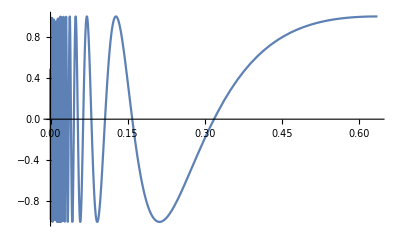
{{-1.,-Graphics-},{-0.5,-Graphics-},{0.,-Graphics-},{0.5,-Graphics-},{1.,-Graphics-},{1.5,-Graphics-},{2.,-Graphics-},{2.5,-Graphics-},{3.,-Graphics-},{3.5,-Graphics-},{4.,-Graphics-},{4.5,-Graphics-},{5.,-Graphics-},{5.5,-Graphics-},{6.,-Graphics-},{6.5,-Graphics-},{7.,-Graphics-},{7.5,-Graphics-},{8.,-Graphics-},{8.5,-Graphics-},{9.,-Graphics-},{9.5,-Graphics-},{10.,-Graphics-}}

```mathematica
Table[{x,Plot[Sin[1/x],{x,0, 2/Pi},AxesOrigin->{0,0}]},{x,-1,10,0.5}]
```

```mathematica
(* 86. ∫_0^(2/ℼ) x Sin 1/x ⅆx *)
Table[{x,NIntegrate[ x Sin[1/x],{x, 0, 2/Pi}]},{x,1,7,0.2}]
```

{{1.,0.102625},{1.2,0.102625},{1.4,0.102625},{1.6,0.102625},{1.8,0.102625},{2.,0.102625},{2.2,0.102625},{2.4,0.102625},{2.6,0.102625},{2.8,0.102625},{3.,0.102625},{3.2,0.102625},{3.4,0.102625},{3.6,0.102625},{3.8,0.102625},{4.,0.102625},{4.2,0.102625},{4.4,0.102625},{4.6,0.102625},{4.8,0.102625},{5.,0.102625},{5.2,0.102625},{5.4,0.102625},{5.6,0.102625},{5.8,0.102625},{6.,0.102625},{6.2,0.102625},{6.4,0.102625},{6.6,0.102625},{6.8,0.102625},{7.,0.102625}}

```mathematica
(* The integral converges when p>1 *)
```

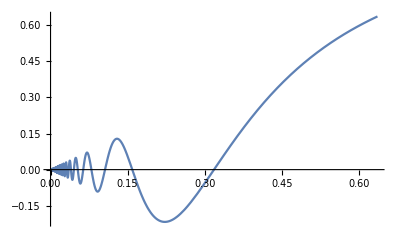
{{1.,-Graphics-},{1.2,-Graphics-},{1.4,-Graphics-},{1.6,-Graphics-},{1.8,-Graphics-},{2.,-Graphics-},{2.2,-Graphics-},{2.4,-Graphics-},{2.6,-Graphics-},{2.8,-Graphics-},{3.,-Graphics-},{3.2,-Graphics-},{3.4,-Graphics-},{3.6,-Graphics-},{3.8,-Graphics-},{4.,-Graphics-},{4.2,-Graphics-},{4.4,-Graphics-},{4.6,-Graphics-},{4.8,-Graphics-},{5.,-Graphics-},{5.2,-Graphics-},{5.4,-Graphics-},{5.6,-Graphics-},{5.8,-Graphics-},{6.,-Graphics-},{6.2,-Graphics-},{6.4,-Graphics-},{6.6,-Graphics-},{6.8,-Graphics-},{7.,-Graphics-}}

```mathematica
Table[{x,Plot[x Sin[1/x],{x,0, 2/Pi},AxesOrigin->{0,0}]},{x,1,7,0.2}]
```